# 6. QRDecomposition

## Matrices with orthogonal columns are useful!

Our target is to construct an orthogonal basis for the column space of a Tall-Skinny m×n matrix
	A=[a_1|a_2|…|a_n].
This basis is naturally represented by a Tall-Skinny m×n matrix
	Q=[q_1|q_2|…|q_n].
We will learn how to compute the QR decomposition A=Q.R where the new matrix R (which tells us how to combine the columns of A to compute Q) is upper triangular!

Every software package has a QR decomposition.  Different packages return the bits in different ways! Always read the documentation and check! Mathematica returns Q on its side!

{9.73976×10^-16,7.54477×10^-16}

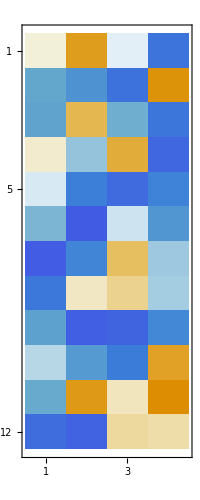
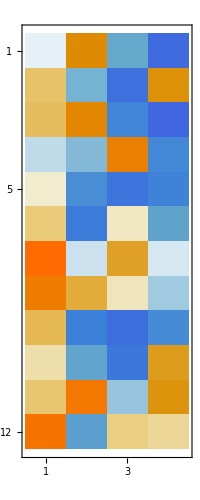
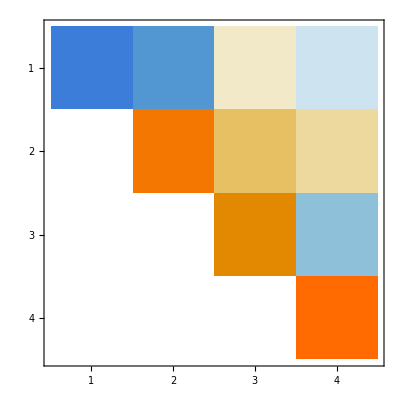

```mathematica
{m,n}={12,4};
A=RandomReal[{-1,1},{m,n}]; 
{Q,R}=QRDecomposition[A];
(* Mathematica #$#@$ returns Q on it side *)
Q=Qᵀ;
Map[Norm,{A-Q.R,Qᵀ.Q-IdentityMatrix[n]}]
Map[MatrixPlot,{A,Q,R}]
```

We are going to learn one way the computer could do this.  Well actually we are going to learn a bunch but the first one is called the Gram-Schmidt process.

## Gram-Schmidt: Idea

The motto here is start at the very beginning of
	A=[a_1|a_2|…|a_n]
and work through the columns!

First, normalize the first column by dividing by ||a_1|| and define
	q_1=a_1/(||a_1||).

Next, project out the component of a_2 in the direction of q_1
	q_2=a_2-(a_2.q_1)q_1
and normalize
	q_2=q_2/||q_2||.
Note we have recycled q_2 repeatedly to accumulate the correct expression.

The next step is more of the same but we need to get a bit more organized!  Pick the next column
	w=a_3
project out the components in q_1 and q_2
	w | = | w-(w.q_1)q_1
w | = | w-(w.q_2)q_2
and normalize
	q_3=w/||w||.
I am using w as mnemonic for work vector!

The next step is more of the same but we need to get a bit more organized!  Pick the next column
	w=a_4
project out the components in q_1 and q_2
	w | = | w-(w.q_1)q_1
w | = | w-(w.q_2)q_2
w | = | w-(w.q_3)q_3
and normalize
	q_4=w/||w||.

All we have to do is keep going until we run out of columns!  We are left with the tall-skinny matrix Q.  The only problem is we do not have the recipe for how we combined the columns: it is in all the work vector w inner products and scalings.

## Gram-Schmidt: Manual

Here is a hand walk through of for a three column matrix! I am saving the coefficients so that we can see where they go!

```mathematica
{m,n}={5,3};
A=RandomReal[{-1,1},{m,n}];
(* First column *)
 v=A⟦All,1⟧;
c1=Norm[v];
q1 =v/c1;
(* second column *)
v=A⟦All,2⟧;
c21 =v.q1;
v=v-c21 q1;
c2=Norm[v];
q2 =v/c2;
(* Third column *)
v=A⟦All,3⟧;
c31 =v.q1;
v=v-c31 q1;
c32 =v.q2;
v=v-c32 q2;
c3=Norm[v];
q3 =v/c3;
MyQ={q1,q2,q3};
{c1,{c21,c2},{c31,c32,c3}}
```

{1.68643,{0.880318,1.15414},{0.605782,-0.440011,0.220694}}

Lets compare to the built-in QR

```mathematica
{BuiltInQ,BuiltInR}=QRDecomposition[A];
BuiltInR
```

{{1.78638,-0.166597,0.919894},{0.,1.12676,0.13323},{0.,0.,0.769686}}

Our numbers match and I think we know how to construct R

## Gram-Schmidt: Script

Here is a preliminary script!

{1.12771×10^-16,3.67581×10^-16}

{True,True}

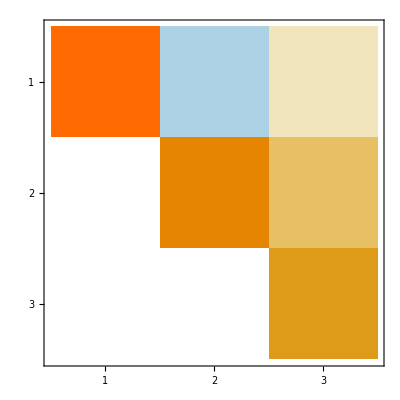

```mathematica
{m,n}={5,3};
A=RandomReal[{-1,1},{m,n}];
(* Set up Storage *)
Q=0*A; R=ConstantArray[0,{n,n}];
(* Loop through columns *)
Do[
(* Grab next column *)
v=A⟦All,j⟧;
(* project out previous columns *)
Do[
R⟦i,j⟧=v.Q⟦All,i⟧;
v=v-R⟦i,j⟧ Q⟦All,i⟧,
{i,1,j-1}];
(* Scale and save orthogonalized columns *)
R⟦j,j⟧=Norm[v];
Q⟦All,j⟧=v/R⟦j,j⟧;,
{j,1,n}]
(* Check that we computed a QR Decomposition *)
Map[Norm,{A-Q.R,Qᵀ.Q-IdentityMatrix[n]}]
{OrthogonalMatrixQ[Q],UpperTriangularMatrixQ[R]}
MatrixPlot[R]
```

## Gram-Schmidt: Function

Here is a function to hide all the crud!

```mathematica
MyGramSchmidt[A_]:= Module[{m,n,Q,R,v},
{m,n}=Dimensions[A];
(* Set up Storage *)
Q=0*A; R=ConstantArray[0,{n,n}];
(* Loop through columns *)
Do[
(* Grab next column *)
v=A⟦All,j⟧;
(* project out previous columns *)
Do[
R⟦i,j⟧=v.Q⟦All,i⟧;
v=v-R⟦i,j⟧ Q⟦All,i⟧,
{i,1,j-1}];
(* Scale and save orthogonalized columns *)
R⟦j,j⟧=Norm[v];
Q⟦All,j⟧=v/R⟦j,j⟧;,
{j,1,n}];
{Q,R}]
```

Here is a test

```mathematica
{m,n}={15,11};
A=RandomReal[{-1,1},{m,n}];
{Q,R}=MyGramSchmidt[A];
(* Check that we computed a QR Decomposition *)
Map[Norm,{A-Q.R,Qᵀ.Q-IdentityMatrix[n]}]
UpperTriangularMatrixQ[R]
```

{6.38596×10^-16,1.10968×10^-15}

True

## Efficiency: Math Libraries

The built in QR decomposition is going to be MUCH faster than any code we write. The reason is that the basic QR computation is the foundation for a lot of other fancier computations.  As a result, a substantial effort has been made to make it as efficient as possible.  This includes economizing storage and computation and communication.

All the higher level tools rely on libraries of math functions.  The lowest level is called BLAS for Basic Linear Algebra Subprograms which are designed to squeeze every possible bit of performance out of all sorts of hardware.

One of the reasons Julia is fast (the Julia folks word is performant) and one of the reasons we are using Julia is that it makes it easy to access these libraries. Good code uses these libraries!